```mathematica
Table[i,{i,0,0.002/0.5,0.002/0.5/14}]
reac={0,-1288.1,-1679.1,-1825.6,-1864.9,-1877.8,-1883.1,-1885.5,-1886.8,-1887.7,-1888.2,-1888.6,-1889,-1889.2,-1889.4}
pl=Table[{Table[i,{i,0,0.002/0.5,0.002/0.5/14}][[i]],-reac[[i]]/480},{i,1,Length[reac]}]
ListLinePlot[pl]
```

```mathematica
980/Sqrt[3.]
```

565.803

{{0.,0.},{0.000285714,3.39167},{0.000571429,4.43516},{0.000857143,4.84141},{0.00114286,4.95339},{0.00142857,4.98984},{0.00171429,5.00495},{0.002,5.01198},{0.00228571,5.01563},{0.00257143,5.01797},{0.00285714,5.01953},{0.00314286,5.02057},{0.00342857,5.02161},{0.00371429,5.02214},{0.004,5.02266}}

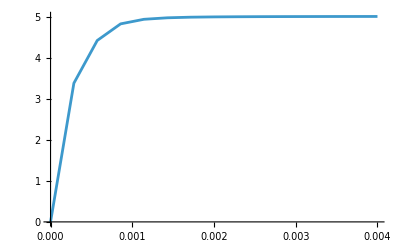

{{0.,0},{0.000285714,2.68354},{0.000571429,3.49813},{0.000857143,3.80333},{0.00114286,3.88521},{0.00142857,3.91208},{0.00171429,3.92312},{0.002,3.92813},{0.00228571,3.93083},{0.00257143,3.93271},{0.00285714,3.93375},{0.00314286,3.93458},{0.00342857,1889/480},{0.00371429,3.93583},{0.004,3.93625}}

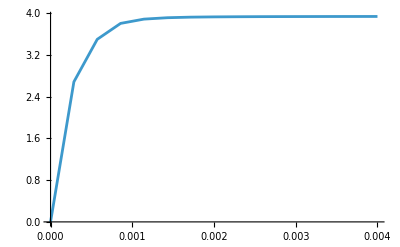

```mathematica
tab=Import["/home/diogo/projects/neopz-master-build-debug/Projects2/PlasticityTestsTresca/loadsweep.csv"];
pl=Table[{Table[i,{i,0,0.002/0.5,0.002/0.5/14}][[i]],-5Transpose[tab][[9]][[i+1]]/(2 960)},{i,1,Length[reac]}]
ListLinePlot[pl]
```

```mathematica
460 5. 0.5
```

1150.

```mathematica
1900. 5
```

9500.

```mathematica
XX=1;XY=2;XZ=3;YY=4;YZ=5;ZZ=6;
subst={200000,0.3,200};
subst2={200000,0.3,200};
ComputeKG[subst_]:=Block[{K,G,young,nu,sigy},
{young,nu,sigy}=subst;
K=young/(3(1-2nu));
G=young/(2(1+nu));
{K,G}
]

Cmat=Table[0,{6},{6}];
Cmatrix[subst_]:=Block[{Cmat=Table[0,{6},{6}],c1,c2,c12,K,G,young,nu,phi,c},
{K,G}=ComputeKG[subst];
c1=(4 G)/3+K;
c12=-((2 G)/3)+K;
c2=G;
Cmat[[XX,XX]]=c1;Cmat[[XX,YY]]=c12;Cmat[[XX,ZZ]]=c12;
Cmat[[YY,XX]]=c12;Cmat[[YY,YY]]=c1;Cmat[[YY,ZZ]]=c12;
Cmat[[ZZ,XX]]=c12;Cmat[[ZZ,YY]]=c12;Cmat[[ZZ,ZZ]]=c1;
Cmat[[XY,XY]]=c2;Cmat[[XZ,XZ]]=c2;Cmat[[YZ,YZ]]=c2;
Return[Cmat]
]
FromVoigtToCart[v_]:={{v[[XX]],v[[XY]],v[[XZ]]},{v[[XY]],v[[YY]],v[[YZ]]},{v[[XZ]],v[[YZ]],v[[ZZ]]}};
FromCartToVoigt[T_]:={T[[1,1]],T[[1,2]],T[[1,3]],T[[2,2]],T[[2,3]],T[[3,3]]};
FromCartToVoigtGrad[T_]:={T[[1,1]], 2T[[1,2]], 2T[[1,3]],T[[2,2]], 2T[[2,3]],T[[3,3]]};
RandomPertubation[tensor_]:=Block[{i,j,delta,tensorint=tensor,sz},
sz=Length[tensorint];
For[i=1,i<=sz,i++,
If[Abs[tensorint[[i]]]<10^-12,Continue[]];
For[j=1,j<=sz,j++,
delta=tensorint[[i]]-tensorint[[j]];
If[delta>10^-12,
tensorint[[i]]+=10^-12;
]
];
];
tensorint
]
EigenSystem[m_]:=Block[{epstprincipalvals,epstprincipaldir,orderedvalues,index,oderedvectors,cart},
cart=FromVoigtToCart[m];
{epstprincipalvals,epstprincipaldir}=Eigensystem[cart];
orderedvalues=Sort[epstprincipalvals,Greater];
index=Table[Position[epstprincipalvals,orderedvalues[[i]]],{i,1,3}]//Flatten;
oderedvectors=Table[epstprincipaldir[[index[[i]]]],{i,1,3}];
{orderedvalues,oderedvectors}
]
PhiPrincipal[{s1_,s2_,s3_},sigy_]:=s1-s3-sigy;
ComputeLambdaSigmaMain3[{sig1tr_,sig2tr_,sig3tr_},subst_]:=Block[{epstr,grad,ss,phimc,K,G,f1,a1,Cep,s2,s3,s1,a,dl1,sigpr,young,nu,sigy},
ss={s1,s2,s3};
Cep={{K+4G/3,K-2G/3,K-2G/3},{K-2G/3,K+4G/3,K-2G/3},{K-2G/3,K-2G/3,K+4G/3}};
sigpr={1/2 (s1+s3+sigy),s2,1/2 (s1+s3-sigy)}//N;
grad=({{1/2, 0, 1/2}, {0, 1, 0}, {1/2, 0, 1/2}});
epstr=Inverse[Cep].ss;
{K,G}=ComputeKG[subst];
{young,nu,sigy}=subst;
{s1,s2,s3}={sig1tr,sig2tr,sig3tr};
{sigpr,grad,epstr}
]

ComputeLambdaSigmaLeft3[{sig1tr_,sig2tr_,sig3tr_},subst_]:=Block[{epstr,grad,young,nu,phi,c,ss,phimc,K,G,f1,f2,a1,Cep,s2,s3,s1,a,dl1,b,d,dl2,left,a2,sigy},
ss={s1,s2,s3};
Cep={{K+4G/3,K-2G/3,K-2G/3},{K-2G/3,K+4G/3,K-2G/3},{K-2G/3,K-2G/3,K+4G/3}};
left={1/3 (s1+s2+s3+sigy),1/3 (s1+s2+s3+sigy),1/3 (s1+s2+s3-2 sigy)}//N;
grad=({{1/3, 1/3, 1/3}, {1/3, 1/3, 1/3}, {1/3, 1/3, 1/3}});
epstr=Inverse[Cep].ss;
{K,G}=ComputeKG[subst];
{young,nu,sigy}=subst;
{s1,s2,s3}={sig1tr,sig2tr,sig3tr};
{left,grad,epstr}
]
ComputeLambdaSigmaRigth3[{sig1tr_,sig2tr_,sig3tr_},subst_]:=Block[{epstr,grad,young,nu,sigy,ss,phimc,K,G,f1,f2,a1,Cep,s2,s3,s1,a,dl1,b,d,dl2,rigth,a2},
ss={s1,s2,s3};
Cep={{K+4G/3,K-2G/3,K-2G/3},{K-2G/3,K+4G/3,K-2G/3},{K-2G/3,K-2G/3,K+4G/3}};
rigth={1/3 (s1+s2+s3+2 sigy),1/3 (s1+s2+s3-sigy),1/3 (s1+s2+s3-sigy)}//N;
grad=({{1/3, 1/3, 1/3}, {1/3, 1/3, 1/3}, {1/3, 1/3, 1/3}});
epstr=Inverse[Cep].ss;
{K,G}=ComputeKG[subst];
{young,nu,sigy}=subst;
{s1,s2,s3}={sig1tr,sig2tr,sig3tr};
{rigth,grad,epstr}
]

EBasisGrad[k_]:=Switch[k,
XX,{{1,0,0},{0,0,0},{0,0,0}},
XY,{{0,1/2,0},{1/2,0,0},{0,0,0}},
XZ,{{0,0,1/2},{0,0,0},{1/2,0,0}},
YY,{{0,0,0},{0,1,0},{0,0,0}},
YZ,{{0,0,0},{0,0,1/2},{0,1/2,0}},
ZZ,{{0,0,0},{0,0,0},{0,0,1}}
];

(*Compute2Grad[solproj,Q,NvecPrincipal[solproj],GradNPrincipal[solproj]]*)
ApplyStrainComputeSigmaDepMainPlane3[epst_,epsp_,alphan_,substin_]:=Block[{epstr3,gradsig3x3,Cmat,subst=substin,Dep,R,vecT,GradN2,a1,nprojhat,nprojrecon,solprojrecon,solprojhat,B,Q,epsetr,sigtr,strhw,vecss,sig1tr,sig2tr,sig3tr,Δγ,sigproj,anlphan1,bool,young,nu,sigy},
{young,nu,sigy}=subst;
Cmat=Cmatrix[subst];
epsetr=epst-epsp;
sigtr=Cmat.epsetr;
{strhw,vecss}=EigenSystem[sigtr];
{sigproj,gradsig3x3,epstr3}=ComputeLambdaSigmaMain3[strhw,subst];
solprojrecon=FromCartToVoigt[Sum[sigproj[[i]]Outer[Times,vecss[[i]],vecss[[i]] ],{i,1,3}]];
Dep=ComputedDep3[strhw,sigproj,epstr3,gradsig3x3,vecss,Cmat,subst];
anlphan1=alphan+Δγ;
If[((sigproj[[1]]>=sigproj[[2]]||Abs[sigproj[[1]]-sigproj[[2]]]<10^-12)&&(sigproj[[2]]>=sigproj[[3]]||Abs[sigproj[[2]]-sigproj[[3]]]<10^-12)),bool=True,bool=False];
{solprojrecon,Dep,anlphan1,bool}
]
ApplyStrainComputeSigmaDepLeftCorner3[epst_,epsp_,alphan_,substin_]:=Block[{grad3x3,epstr3,young,nu,sigy,Cmat,subst=substin,ZaaZ,ZabZ,ZbaZ,ZbbZ,Z,q,a,b,d,nprojrecon2,nprojrecon1,Dep,R,vecT,GradN21,GradN22,a1,a2,nprojhat,nprojrecon,solprojrecon,solprojhat,B,Q,epsetr,sigtr,strhw,vecss,sig1tr,sig2tr,sig3tr,Δγ1,Δγ2,sigproj,anlphan1,et2,T,bool},
Cmat=Cmatrix[subst];
{young,nu,sigy}=subst;
epsetr=epst-epsp;
sigtr=Cmat.epsetr;
{strhw,vecss}=EigenSystem[sigtr];
vecT=Transpose[vecss];
{strhw,vecss}=EigenSystem[sigtr];
{sigproj,grad3x3,epstr3}=ComputeLambdaSigmaLeft3[strhw,subst];
solprojrecon=FromCartToVoigt[Sum[sigproj[[i]]Outer[Times,vecss[[i]],vecss[[i]] ],{i,1,3}]];
Dep=ComputedDep3[strhw,sigproj,epstr3,grad3x3,vecss,Cmat,subst];
If[((sigproj[[1]]>=sigproj[[2]]||Abs[sigproj[[1]]-sigproj[[2]]]<10^-12)&&(sigproj[[2]]>=sigproj[[3]]||Abs[sigproj[[2]]-sigproj[[3]]]<10^-12)),bool=True,bool=False];
{solprojrecon,Dep,anlphan1,bool}
]

ApplyStrainComputeSigmaDepRigthCorner3[epst_,epsp_,alphan_,substin_]:=Block[{sigy,grad3x3,epstr3,young,nu,phi,c,Cmat,subst=substin,ZaaZ,ZabZ,ZbaZ,ZbbZ,Z,q,a,b,d,nprojrecon2,nprojrecon1,Dep,R,vecT,GradN21,GradN22,a1,a2,nprojhat,nprojrecon,solprojrecon,solprojhat,B,Q,epsetr,sigtr,strhw,vecss,sig1tr,sig2tr,sig3tr,Δγ1,Δγ2,sigproj,anlphan1,et2,T,bool},
Cmat=Cmatrix[subst];
{young,nu,sigy}=subst;
(*Print[Cmat//MatrixForm];*);
epsetr=epst-epsp;
sigtr=Cmat.epsetr;
{strhw,vecss}=EigenSystem[sigtr];
vecT=Transpose[vecss];
(*Print["sigtr = ",sigtr];*);
{strhw,vecss}=EigenSystem[sigtr];
{sigproj,grad3x3,epstr3}=ComputeLambdaSigmaRigth3[strhw,subst];

solprojrecon=FromCartToVoigt[Sum[sigproj[[i]]Outer[Times,vecss[[i]],vecss[[i]] ],{i,1,3}]];
Dep=ComputedDep3[strhw,sigproj,epstr3,grad3x3,vecss,Cmat,subst];
If[((sigproj[[1]]>=sigproj[[2]]||Abs[sigproj[[1]]-sigproj[[2]]]<10^-12)&&(sigproj[[2]]>=sigproj[[3]]||Abs[sigproj[[2]]-sigproj[[3]]]<10^-12)),bool=True,bool=False];
{solprojrecon,Dep,anlphan1,bool}
];
ComputedDep3[sigPtr_,sigPproj_,EpsPtr_,Dproj_,EigenVecs_,Ce6_,subst_]:=Block[{fac,colrot,Sij,mat,icol,δE,i,j,G,λ,young ,nu,col,R,projii,projjj,tempmat,depstr,dsigproj,tempscalar,tempmat2},
young=subst[[1]];
nu=subst[[2]];
G=young /(2(1+nu));
λ=young nu /((1+nu)(1-2 nu));
mat=Table[0,{6}];
R=Table[0,{6},{6}];

For[icol=1,icol<=6,icol++,
δE=EBasisGrad[icol];
colA=Table[0,{6}];
colR=Table[0,{6}];
For[i=1,i<=3,i++,
For[j=1,j<=3,j++,
projii=FromCartToVoigt[Outer[Times,EigenVecs[[i]],EigenVecs[[i]]]];
projjj=FromCartToVoigtGrad[Outer[Times,EigenVecs[[j]],EigenVecs[[j]]]];
tempmat=Outer[Times,projii,projjj];
tempmat=((Dproj[[i,j]]tempmat).Ce6).W.FromCartToVoigt[δE];
colA+=tempmat;
If[j<=i,Continue[];];
depstr=(EpsPtr[[i]]-EpsPtr[[j]]);
dsigproj=(sigPproj[[i]]-sigPproj[[j]]) ;
If[(Abs[depstr])<10^-12,
(*autovalores repetidos*)
fac=G (Dproj[[i,i]]-Dproj[[i,j]]-Dproj[[j,i]]+Dproj[[j,j]]);
,
fac=dsigproj/depstr;
];
Sij=1/2(Outer[Times,EigenVecs[[i]],EigenVecs[[j]]]+Outer[Times,EigenVecs[[j]],EigenVecs[[i]]]);
sij=FromCartToVoigt[Sij];
sji=FromCartToVoigtGrad[Sij];
tempmat=Outer[Times,sij,sji];
colR+=2fac tempmat.FromCartToVoigt[δE];
(*tempscalar=EigenVecs[[j]].(δE.EigenVecs[[i]]);
tempmat2=(Outer[Times,EigenVecs[[i]],EigenVecs[[j]]]+Outer[Times,EigenVecs[[j]],EigenVecs[[i]]]);
colR+=FromCartToVoigt[ fac tempscalar tempmat2];*)
];
];
mat[[icol]]=colA;
R[[icol]]=colR;
];
mat+=R;
mat
];

W=DiagonalMatrix[{1,2,2,1,2,1}];
ProjectStress[epsttr_,epsptr_,alphan_,subst_]:=Block[{young,nu,sigy,valcheck,phimain,sig,dep,alp,Cmat,epsetr,sigtr,strhw,vecss,bool},
Cmat=Cmatrix[subst];
{young,nu,sigy}=subst;
epsetr=epsttr-epsptr;
sigtr=Cmat.epsetr;

{strhw,vecss}=EigenSystem[sigtr];

phimain=PhiPrincipal[strhw,sigy];
(*{sig,dep,alp}=ApplyStrainComputeSigmaDepMainPlane[epsttr,epsptr,alphan,subst];*)
If[phimain<0,(*elastico*)
Return[{sigtr,Cmat,alphan,0}]
];
(*{sig,dep,alp,bool}=ApplyStrainComputeSigmaDepMainPlane[epsttr,epsptr,alphan,subst];*);
{sig,dep,alp,bool}=ApplyStrainComputeSigmaDepMainPlane3[epsttr,epsptr,alphan,subst];
If[bool==True,
Return[{sig,dep,alp,1}];
,
(*Print["strhw = ",strhw];*)
valcheck=strhw[[1]]+strhw[[3]]-2 strhw[[2]];
(*Print["valcheck = ", valcheck];*);
If[valcheck>0,
{sig,dep,alp,bool}=ApplyStrainComputeSigmaDepRigthCorner3[epsttr,epsptr,alphan,subst];
(*{sig,dep,alp,bool}=ApplyStrainComputeSigmaDepRigthCorner[epsttr,epsptr,alphan,subst];*);
If[bool==True,
Return[{sig,dep,alp,2}];
];
,
(*{sig,dep,alp,bool}=ApplyStrainComputeSigmaDepLeftCorner[epsttr,epsptr,alphan,subst];*)
{sig,dep,alp,bool}=ApplyStrainComputeSigmaDepLeftCorner3[epsttr,epsptr,alphan,subst];
If[bool==True,
Return[{sig,dep,alp,3}];
];
];
Print["FALHOU TODOS"];
Return[{sig,dep,alp,0}];
];
];
```

```mathematica
epsttr={3.6157562487484481 10^-2,(2.5111726131341262) 10^-2,0,-2.5800526093809846 10^-2,0,0};
epsptr={0,0,0,0,0,0};
(*{sig,dep,alp,bool}=ApplyStrainComputeSigmaDepMainPlane[epsttr,epsptr,0,subst];*)
{sig,dep,alp,v}=ProjectStress[epsttr,epsptr,0,subst];
Print["type = ",v];
sig//MatrixForm
dep//MatrixForm
```

type = 2

(1852.18
37.5623
0.
1666.83
0.
1659.51)

(166878. | -520.715 | 0. | 166456. | 0. | 166667.
-520.715 | 1284.76 | 0. | 520.715 | 0. | 0.
0. | 0. | 2495.48 | 0. | 486.491 | 0.
166456. | 520.715 | 0. | 166878. | 0. | 166667.
0. | 0. | 486.491 | 0. | 94.841 | 0.
166667. | 9.09495×10^-13 | 0. | 166667. | 0. | 166667.)

```mathematica
({{166877.71347131103, -520.7151650413412, 0., 166455.6198620223, 0., 166666.66666666666}, {-520.7151650413404, 1284.7590067091674, 0., 520.7151650413404, 0., 0.}, {0., 0., 2495.475799905083, 0., 486.4908351665485, 0.}, {166455.61986202226, 520.7151650413402, 0., 166877.713471311, 0., 166666.66666666666}, {0., 0., 486.4908351665485, 0., 94.84096488134561, 0.}, {166666.66666666666, 9.094947017729282*^-13, 0., 166666.66666666666, 0., 166666.66666666666}})
```

{{166878.,-520.715,0.,166456.,0.,166667.},{-520.715,1284.76,0.,520.715,0.,0.},{0.,0.,2495.48,0.,486.491,0.},{166456.,520.715,0.,166878.,0.,166667.},{0.,0.,486.491,0.,94.841,0.},{166667.,9.09495×10^-13,0.,166667.,0.,166667.}}

```mathematica
epsttr={-7.1436465404952029 10^-5,(3.7632073167565092) 10^-4,0,-5.4913608546659984 10^-5,0,1.1423294530637051 10^-4};
epsptr={0,0,0,0,0,0};
(*{sig,dep,alp,bool}=ApplyStrainComputeSigmaDepLeftCorner[epsttr,epsptr,0,subst2];
sig//MatrixForm
dep//MatrixForm*)
{sig,dep,alp,v}=ProjectStress[epsttr,epsptr,0,subst2];
Print["type = ",v];
sig//MatrixForm
dep//MatrixForm
```

type = 0

(-12.3884
28.9477
0.
-9.84638
0.
16.1762)

(269231. | 0 | 0 | 115385. | 0 | 115385.
0 | 76923.1 | 0 | 0 | 0 | 0
0 | 0 | 76923.1 | 0 | 0 | 0
115385. | 0 | 0 | 269231. | 0 | 115385.
0 | 0 | 0 | 0 | 76923.1 | 0
115385. | 0 | 0 | 115385. | 0 | 269231.)

```mathematica
({{2.1701841541531123*^7, -6.100068325307025*^6, 0., 1.4817548840291232*^7, 0., 1.2014511624632746*^7}, {-6.100068325307025*^6, 2.106465996765339*^6, 0., -6.193838940884006*^6, 0., -4.044571670487953*^6}, {0., 0., 3.32139848735755*^6, 0., 54533.00939941033, 0.}, {1.4817548840291217*^7, -6.193838940884006*^6, 0., 2.06222811937187*^7, 0., 1.1659347143170252*^7}, {0., 0., 54533.00939941033, 0., 3.3261871744136484*^6, 0.}, {1.2014511624632746*^7, -4.044571670487953*^6, 0., 1.1659347143170267*^7, 0., 7.788461099483669*^6}})
```

{{2.17018×10^7,-6.10007×10^6,0.,1.48175×10^7,0.,1.20145×10^7},{-6.10007×10^6,2.10647×10^6,0.,-6.19384×10^6,0.,-4.04457×10^6},{0.,0.,3.3214×10^6,0.,54533.,0.},{1.48175×10^7,-6.19384×10^6,0.,2.06223×10^7,0.,1.16593×10^7},{0.,0.,54533.,0.,3.32619×10^6,0.},{1.20145×10^7,-4.04457×10^6,0.,1.16593×10^7,0.,7.78846×10^6}}

```mathematica
(*RIGTH*)
epsttr={2.1153582845979804 10^-2,-6.1244636739267791 10^-3,0,0,0,(-3.2774022989690031) 10^-2};
epsttr={2.1153582845979804 10^-2,(-3.2774022989690031) 10^-2,0,-6.1244636739267791 10^-3,0,0};
epsptr={0,0,0,0,0,0};
(*{sig,dep,alp}=ApplyStrainComputeSigmaDepRigthCorner[epsttr,epsptr,0,subst];
sig//MatrixForm
dep//MatrixForm*)
{sig,dep,alp,v}=ProjectStress[epsttr,epsptr,0,subst];
Print["type = ",v];
sig//MatrixForm
dep//MatrixForm
```

type = 2

(2602.16
-76.8609
0.
2474.21
0.
2438.19)

(168052. | 1153.11 | 0. | 165281. | 0. | 166667.
1153.11 | 959.741 | 0. | -1153.11 | 0. | -3.63798×10^-12
0. | 0. | 2843.29 | 0. | -1332.78 | 0.
165281. | -1153.11 | 0. | 168052. | 0. | 166667.
0. | 0. | -1332.78 | 0. | 624.731 | 0.
166667. | -1.09139×10^-11 | 0. | 166667. | 0. | 166667.)

```mathematica
({{22636.70307235705, 7618.6086955898345, 0., 35310.4378582731, 0., 38883.11518851569}, {7618.608695595771, 2564.7220071261327, 0., 11880.966638762142, 0., 13084.411442502547}, {0., 0., 1214.0332633996193, 0., 2576.8648275442256, 0.}, {35310.43785828294, 11880.966638756187, 0., 55095.96651134384, 0., 60663.6078748391}, {0., 0., 2576.8648275442256, 0., 5503.518180364142, 0.}, {38883.11518852395, 13084.411442496683, 0., 60663.607874837646, 0., 66796.85377654125}})
```

{{22636.7,7618.61,0.,35310.4,0.,38883.1},{7618.61,2564.72,0.,11881.,0.,13084.4},{0.,0.,1214.03,0.,2576.86,0.},{35310.4,11881.,0.,55096.,0.,60663.6},{0.,0.,2576.86,0.,5503.52,0.},{38883.1,13084.4,0.,60663.6,0.,66796.9}}

```mathematica
epsttr={5.3478453422430648 10^-2,(-1.5617788046085865) 10^-2,0,-2.9697679208221188 10^-2,0,0};
epsptr={0,0,0,0,0,0};
(*{sig,dep,alp}=ApplyStrainComputeSigmaDepRigthCorner[epsttr,epsptr,0,subst];
sig//MatrixForm
dep//MatrixForm*)
{sig,dep,alp,v}=ProjectStress[epsttr,epsptr,0,subst];
Print["type = ",v];
sig//MatrixForm
dep//MatrixForm
```

type = 2

(4095.08
-18.4543
0.
3898.51
0.
3896.8)

(166707. | 214.314 | 0. | 166626. | 0. | 166667.
214.314 | 1141.38 | 0. | -214.314 | 0. | 0.
0. | 0. | 1829. | 0. | -170.226 | 0.
166626. | -214.314 | 0. | 166707. | 0. | 166667.
0. | 0. | -170.226 | 0. | 15.843 | 0.
166667. | 9.09495×10^-13 | 0. | 166667. | 0. | 166667.)

```mathematica
epsttr={-8.3333333333333835 10^-3,(-4.3368086899420177) 10^-18,0,8.0065359477124644 10^-3,0,0};
epsptr={0,0,0,0,0,0};
(*{sig,dep,alp}=ApplyStrainComputeSigmaDepRigthCorner[epsttr,epsptr,0,subst];
sig//MatrixForm
dep//MatrixForm*)
{sig,dep,alp,v}=ProjectStress[epsttr,epsptr,0,subst];
Print["type = ",v];
sig//MatrixForm
dep//MatrixForm
```

type = 1

(-162.846
-2.65413×10^-14
0.
37.1543
0.
-37.7074)

(192308. | -1.62433×10^-12 | 0. | 192308. | 0. | 115385.
-1.62433×10^-12 | 6120. | 0. | 1.62433×10^-12 | 0. | 0.
0. | 0. | 7508.3 | 0. | 3.75991×10^-13 | 0.
192308. | 1.62433×10^-12 | 0. | 192308. | 0. | 115385.
0. | 0. | 3.75991×10^-13 | 0. | 4675.04 | 0.
115385. | 0. | 0. | 115385. | 0. | 269231.)

```mathematica
epsttr={-1.2059120385099618 10^-4,(3.3357327520074689) 10^-4,0,-7.4841702105660107 10^-6,0,1.0838886807601270 10^-4};
epsptr={0,0,0,0,0,0};
(*{sig,dep,alp}=ApplyStrainComputeSigmaDepRigthCorner[epsttr,epsptr,0,subst];
sig//MatrixForm
dep//MatrixForm*)
{sig,dep,alp,v}=ProjectStress[epsttr,epsptr,0,subst2];
Print["type = ",v];
sig//MatrixForm
dep//MatrixForm
```

type = 0

(-20.824
25.6595
0.
-3.42293
0.
14.4037)

(269231. | 0 | 0 | 115385. | 0 | 115385.
0 | 76923.1 | 0 | 0 | 0 | 0
0 | 0 | 76923.1 | 0 | 0 | 0
115385. | 0 | 0 | 269231. | 0 | 115385.
0 | 0 | 0 | 0 | 76923.1 | 0
115385. | 0 | 0 | 115385. | 0 | 269231.)

```mathematica
epsttr={-7.1436465404952029 10^-5,(3.7632073167565092) 10^-4,0,-5.4913608546659984 10^-5,0,1.1423294530637051 10^-4};
epsptr={0,0,0,0,0,0};
(*{sig,dep,alp}=ApplyStrainComputeSigmaDepRigthCorner[epsttr,epsptr,0,subst];
sig//MatrixForm
dep//MatrixForm*)
{sig,dep,alp,v}=ProjectStress[epsttr,epsptr,0,subst2];
Print["type = ",v];
sig//MatrixForm
dep//MatrixForm
```

type = 0

(-12.3884
28.9477
0.
-9.84638
0.
16.1762)

(269231. | 0 | 0 | 115385. | 0 | 115385.
0 | 76923.1 | 0 | 0 | 0 | 0
0 | 0 | 76923.1 | 0 | 0 | 0
115385. | 0 | 0 | 269231. | 0 | 115385.
0 | 0 | 0 | 0 | 76923.1 | 0
115385. | 0 | 0 | 115385. | 0 | 269231.)

```mathematica
x0
xp
```

x0

xp

```mathematica
Simplify[Log[a x^2]-(Log[a]+2Log[x]),Assumptions->{a>0,x>0}]
```

0

```mathematica
f[x_,xp_]:=ProjectStress[x,xp,0,subst][[1]];
df[x_,xp_]:=ProjectStress[x,xp,0,subst][[2]];
type[x_,xp_]:=ProjectStress[x,xp,0,subst][[4]];

err[α1_?NumericQ,α2_?NumericQ,x00_,xpp_,typecheck_]:=Block[{xp=xpp,x0=x00,dx,f0,g0,gdx,error1,error2,p,state0,scale=1.,tries=0,maxtries=1},(*direção pequena*)
dx=RandomReal[{-1,1},6];
If[Norm[dx]==0.,dx=ConstantArray[1.,6]];
dx=1.*^-3 Normalize[dx];
(*estado base (uma chamada só)*)
state0=ProjectStress[x0,xp,0,subst];
f0=state0[[1]];
g0=state0[[2]];
gdx=g0.dx;
(*garantir que o ponto perturbado mantém o mesmo tipo*)
While[(type[x0+α1 dx,xp]=!=typecheck)||(type[x0+α2 dx,xp]=!=typecheck),
scale=scale/2;
dx=scale dx;
tries++;
If[tries>maxtries,Print["[aviso] tipo errado persistente para type = ",typecheck,". reduzindo falhou."];
Return[{Indeterminate,Indeterminate}];
];
];
(*erros e ordem*)
error1=Abs[f[x0+α1 dx,xp]-(f0+α1 gdx)];
error2=Abs[f[x0+α2 dx,xp]-(f0+α2 gdx)];

If[error1==0||error2==0,
(*recuo do passo se houve cancelamento numérico*)
α1=0.1 α1;α2=0.1 α2;
error1=Abs[f[x0+α1 dx,xp]-(f0+α1 gdx)];
error2=Abs[f[x0+α2 dx,xp]-(f0+α2 gdx)];];
p=N@(Log[error2/error1]/Log[α2/α1]);
{error1,p}
];

(*---busca por par (x0,xp) de um dado type---*)
BuildX[type0_]:=Block[{typeint=100,xp,x0,limit=200,count=0,a,b},
a=-0.005;
b=0.005;
xp=RandomReal[{a,b},6];
x0=RandomReal[{a,b},6];
While[type0=!=typeint&&count<=limit,
xp=RandomReal[{a,b},6];
x0=RandomReal[{a,b},6];
typeint=type[x0,xp];
count++;];
Print["type = ",type0];
{x0,xp}];

(*---varredura e gráficos para tipos 1,2,3---*)
errs3[_]:=Block[{typeint1=1,typeint2=2,typeint3=3,x1,xp1,x2,xp2,x3,xp3,alphas1,alphas2,vecp1={},vecp2={},vecp3={},pts1={},pts2={},pts3={},i,e,p},{x1,xp1}=BuildX[typeint1];
{x2,xp2}=BuildX[typeint2];
{x3,xp3}=BuildX[typeint3];
alphas1=RandomReal[{0.0001,0.01},300];
alphas2=RandomReal[{0.0001,0.01},300];
For[i=1,i<=Length[alphas1],i++,
Print["ialpha = ",i];
{e,p}=err[alphas1[[i]],alphas2[[i]],x1,xp1,typeint1];
AppendTo[vecp1,p];
AppendTo[pts1,{alphas1[[i]],Norm[e,"Frobenius"]}];
{e,p}=err[alphas1[[i]],alphas2[[i]],x2,xp2,typeint2];
AppendTo[vecp2,p];
AppendTo[pts2,{alphas1[[i]],Norm[e,"Frobenius"]}];
{e,p}=err[alphas1[[i]],alphas2[[i]],x3,xp3,typeint3];
AppendTo[vecp3,p];
AppendTo[pts3,{alphas1[[i]],Norm[e,"Frobenius"]}];
];
{vecp1,vecp2,vecp3,pts1,pts2,pts3}
];
```

```mathematica
{vecp1,vecp2,vecp3,pts1,pts2,pts3}=errs3[_];
```

type = 1

type = 2

type = 3

ialpha = 1

ialpha = 2

ialpha = 3

ialpha = 4

ialpha = 5

ialpha = 6

ialpha = 7

ialpha = 8

ialpha = 9

ialpha = 10

ialpha = 11

ialpha = 12

ialpha = 13

ialpha = 14

ialpha = 15

ialpha = 16

ialpha = 17

ialpha = 18

ialpha = 19

ialpha = 20

ialpha = 21

ialpha = 22

ialpha = 23

ialpha = 24

ialpha = 25

ialpha = 26

ialpha = 27

ialpha = 28

ialpha = 29

ialpha = 30

ialpha = 31

ialpha = 32

ialpha = 33

ialpha = 34

ialpha = 35

ialpha = 36

ialpha = 37

ialpha = 38

ialpha = 39

ialpha = 40

ialpha = 41

ialpha = 42

ialpha = 43

ialpha = 44

ialpha = 45

ialpha = 46

ialpha = 47

ialpha = 48

ialpha = 49

ialpha = 50

ialpha = 51

ialpha = 52

ialpha = 53

ialpha = 54

ialpha = 55

ialpha = 56

ialpha = 57

ialpha = 58

ialpha = 59

ialpha = 60

ialpha = 61

ialpha = 62

ialpha = 63

ialpha = 64

ialpha = 65

ialpha = 66

ialpha = 67

ialpha = 68

ialpha = 69

ialpha = 70

ialpha = 71

ialpha = 72

ialpha = 73

ialpha = 74

ialpha = 75

ialpha = 76

ialpha = 77

ialpha = 78

ialpha = 79

ialpha = 80

ialpha = 81

ialpha = 82

ialpha = 83

ialpha = 84

ialpha = 85

ialpha = 86

ialpha = 87

ialpha = 88

ialpha = 89

ialpha = 90

ialpha = 91

ialpha = 92

ialpha = 93

ialpha = 94

ialpha = 95

ialpha = 96

ialpha = 97

ialpha = 98

ialpha = 99

ialpha = 100

ialpha = 101

ialpha = 102

ialpha = 103

ialpha = 104

ialpha = 105

ialpha = 106

ialpha = 107

ialpha = 108

ialpha = 109

ialpha = 110

ialpha = 111

ialpha = 112

ialpha = 113

ialpha = 114

ialpha = 115

ialpha = 116

ialpha = 117

ialpha = 118

ialpha = 119

ialpha = 120

ialpha = 121

ialpha = 122

ialpha = 123

ialpha = 124

ialpha = 125

ialpha = 126

ialpha = 127

ialpha = 128

ialpha = 129

ialpha = 130

ialpha = 131

ialpha = 132

ialpha = 133

ialpha = 134

ialpha = 135

ialpha = 136

ialpha = 137

ialpha = 138

ialpha = 139

ialpha = 140

ialpha = 141

ialpha = 142

ialpha = 143

ialpha = 144

ialpha = 145

ialpha = 146

ialpha = 147

ialpha = 148

ialpha = 149

ialpha = 150

ialpha = 151

ialpha = 152

ialpha = 153

ialpha = 154

ialpha = 155

ialpha = 156

ialpha = 157

ialpha = 158

ialpha = 159

ialpha = 160

ialpha = 161

ialpha = 162

ialpha = 163

ialpha = 164

ialpha = 165

ialpha = 166

ialpha = 167

ialpha = 168

ialpha = 169

ialpha = 170

ialpha = 171

ialpha = 172

ialpha = 173

ialpha = 174

ialpha = 175

ialpha = 176

ialpha = 177

ialpha = 178

ialpha = 179

ialpha = 180

ialpha = 181

ialpha = 182

ialpha = 183

ialpha = 184

ialpha = 185

ialpha = 186

ialpha = 187

ialpha = 188

ialpha = 189

ialpha = 190

ialpha = 191

ialpha = 192

ialpha = 193

ialpha = 194

ialpha = 195

ialpha = 196

ialpha = 197

ialpha = 198

ialpha = 199

ialpha = 200

ialpha = 201

ialpha = 202

ialpha = 203

ialpha = 204

ialpha = 205

ialpha = 206

ialpha = 207

ialpha = 208

ialpha = 209

ialpha = 210

ialpha = 211

ialpha = 212

ialpha = 213

ialpha = 214

ialpha = 215

ialpha = 216

ialpha = 217

ialpha = 218

ialpha = 219

ialpha = 220

ialpha = 221

ialpha = 222

ialpha = 223

ialpha = 224

ialpha = 225

ialpha = 226

ialpha = 227

ialpha = 228

ialpha = 229

ialpha = 230

ialpha = 231

ialpha = 232

ialpha = 233

ialpha = 234

ialpha = 235

ialpha = 236

ialpha = 237

ialpha = 238

ialpha = 239

ialpha = 240

ialpha = 241

ialpha = 242

ialpha = 243

ialpha = 244

ialpha = 245

ialpha = 246

ialpha = 247

ialpha = 248

ialpha = 249

ialpha = 250

ialpha = 251

ialpha = 252

ialpha = 253

ialpha = 254

ialpha = 255

ialpha = 256

ialpha = 257

ialpha = 258

ialpha = 259

ialpha = 260

ialpha = 261

ialpha = 262

ialpha = 263

ialpha = 264

ialpha = 265

ialpha = 266

ialpha = 267

ialpha = 268

ialpha = 269

ialpha = 270

ialpha = 271

ialpha = 272

ialpha = 273

ialpha = 274

ialpha = 275

ialpha = 276

ialpha = 277

ialpha = 278

ialpha = 279

ialpha = 280

ialpha = 281

ialpha = 282

ialpha = 283

ialpha = 284

ialpha = 285

ialpha = 286

ialpha = 287

ialpha = 288

ialpha = 289

ialpha = 290

ialpha = 291

ialpha = 292

ialpha = 293

ialpha = 294

ialpha = 295

ialpha = 296

ialpha = 297

ialpha = 298

ialpha = 299

ialpha = 300

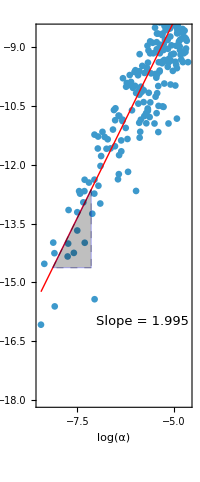

```mathematica
pts=Select[pts1,#[[1]]>0&&#[[2]]>0&];
data=Transpose@{Log[pts[[All,1]]],Log[pts[[All,2]]]};

fit=LinearModelFit[data,x,x];
b1=fit["BestFitParameters"][[2]];      (*slope*)

{xmin,xmax}={Min[data[[All,1]]],Max[data[[All,1]]]};
{ymin,ymax}={Min[data[[All,2]]],Max[data[[All,2]]]};

(*---triângulo colado na reta---*)
base=1.0;
x0=Min[xmin+0.08 (xmax-xmin),xmax-base-0.02 (xmax-xmin)];

p0={x0,fit[x0]};
p1={x0+base,fit[x0+base]};
p2={x0+base,fit[x0]};

theta=ArcTan[b1];

tri={Directive[Opacity[.25]],EdgeForm[{Blue,Thick}],Polygon[{p0,p1,p2}],{Dashed,Black,Thick,Line[{p0,p1}],Line[{p1,p2}],Line[{p2,p0}]},(*rótulo preto,opaco e alinhado à reta*)Rotate[Text[Style[Row[{"Slope = ",NumberForm[b1,{5,3}]}],13,Black,Opacity[1],Background->White],{-5.8,-16.0}],0,{-10,-20}]};

Show[ListPlot[data,PlotRange->All,Frame->True,PlotStyle->Directive[PointSize[.012]]],Plot[fit[x],{x,xmin,xmax},PlotStyle->{Red,Thick}],Epilog->tri,FrameLabel->{Style["log(α)",14,Black],Style["log(||E(α)||)",14,Black]},LabelStyle->Directive[Black,12],FrameStyle->Black,BaseStyle->Black,AspectRatio->Automatic,PlotRange->{{-8.5,-4.6},{-18,-8.6}}]
```